```mathematica
po[n_,s_]:=1/2 s (s-1) Pi^(-s/2) Gamma[s/2] HarmonicNumber[n,s]
pl[n_,s_]:=1/2 s (s-1) Pi^(-s/2) Gamma[s/2] Zeta[s]
```

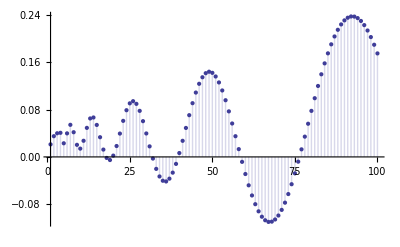

```mathematica
DiscretePlot[Re@po[n,10I],{n,1,100}]
```

```mathematica
FullSimplify[Limit[po[n,s],s->0]]
```

-n

```mathematica
p1[n_,s_]:=(1/2+s)Sum[(n/j)^(1/2-s),{j,1,n}]-(1/2-s)Sum[(n/j)^(1/2+s),{j,1,n}]
p2[n_,s_]:=Sum[(n/j)^(1/2)(2s Cosh[s Log[n/j]]- Sinh[s Log[n/j]]),{j,1,n}]
```

```mathematica
p2[100,.2+8I]
```

117.705+260.386 ⅈ

```mathematica
p1[100,.2+8I]
```

117.705+260.386 ⅈ

```mathematica
p3[n_,s_]:=(1/2+s)Sum[(n/j)^(1/2-s),{j,1,n}]+(1/2-s)Sum[(n/j)^(1/2+s),{j,1,n}]
p4[n_,s_]:=Sum[(n/j)^(1/2)( Cosh[s Log[n/j]]- 2s Sinh[s Log[n/j]]),{j,1,n}]-2n
```

```mathematica
N@p4[10000,-.5+ZetaZero[1]]
```

0.496666+0. ⅈ

```mathematica
N@p4[10000,-2]
```

-2.01223×10^10

```mathematica
p3[100,.2+8I]
```

45.4413-176.352 ⅈ

```mathematica
z1[n_,s_]:=-2n +(1/2+s)(-Sum[(n/j)^(1/2-s),{j,1,n}])+(1/2-s)(-Sum[(n/j)^(1/2+s),{j,1,n}])
```

```mathematica
N@z1[10000,-ZetaZero@1]
```

5990.79-3199.43 ⅈ

```mathematica
h1[n_,s_]:=-n+(1+s)(Sum[(n/j)^(-s),{j,1,n}]-n^-s Zeta[-s])
h2[n_,s_]:=-n+(1+(s-1/2))(Sum[(n/j)^(-(s-1/2)),{j,1,n}]-n^-(s-1/2) Zeta[-(s-1/2)])
h3[n_,s_]:=-n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])
h4[n_,s_]:=-n+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
hadd[n_,s_]:=-n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+-n+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
hsub[n_,s_]:=-n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+n-(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
```

```mathematica
N@(hsub[10000,.8])
```

0.8

```mathematica
(1+(s-1/2))/2/.s->.8
```

0.65

```mathematica
N[h3[n,.8+I]+h4[n,.8+I]/.n->100]
```

$Aborted

```mathematica
hsubx[n_,s_]:=-n+(1/2+s)Sum[(n/j)^(1/2-s),{j,1,n}]+n-(1/2-s)Sum[(n/j)^(1/2+s),{j,1,n}]
```

```mathematica
N@hsubx[100,-.5+ZetaZero@1]
```

0.+14.1347 ⅈ

```mathematica
hsub[n_,s_]:=-n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+n-(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
hsub1[n_,s_]:=(1/2+s)(-n^(1/2-s) Zeta[1/2-s])-(1/2-s)(-n^(1/2+s) Zeta[1/2+s])+
(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}])-(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}])
hsub2[n_,s_]:=(1/2+s)(-n^(1/2-s) Zeta[1/2-s])-(1/2-s)(-n^(1/2+s) Zeta[1/2+s])+
Sum[(n/j)^(1/2)(2s Cosh[s Log[n/j]]- Sinh[s Log[n/j]]),{j,1,n}]
```

```mathematica
hsub2[1000,-.2+3I]
```

-0.2+3. ⅈ

```mathematica
hsub[1000,.2+4I]
```

0.2+4. ⅈ

```mathematica
hadd[n_,s_]:=-n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+-n+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
hadd1[n_,s_]:=-2n+(1/2+s)(-n^(1/2-s) Zeta[1/2-s])+(1/2-s)(-n^(1/2+s) Zeta[1/2+s])+
(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}])+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}])
hadd2[n_,s_]:=-2n+(1/2+s)(-n^(1/2-s) Zeta[1/2-s])+(1/2-s)(-n^(1/2+s) Zeta[1/2+s])+
Sum[(n/j)^(1/2)( Cosh[s Log[n/j]]- 2s Sinh[s Log[n/j]]),{j,1,n}]
```

```mathematica
hadd2[10000,.2+4I]
```

0.49973+0.0000266666 ⅈ

```mathematica
hadd[10000,.2+4I]
```

0.49973+0.0000266667 ⅈ

```mathematica
hsub2x[n_,s_]:=Sum[(n/j)^(1/2)(2s Cosh[s Log[n/j]]- Sinh[s Log[n/j]]),{j,1,n}]
hadd2x[n_,s_]:=-2n+Sum[(n/j)^(1/2)( Cosh[s Log[n/j]]- 2s Sinh[s Log[n/j]]),{j,1,n}]
```

```mathematica
hadd2x[10000,N@Im@ZetaZero@1 I]
```

0.496666+0. ⅈ

```mathematica
hsub2y[n_,s_]:=Sum[(n/j)^(1/2)(2s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]
hadd2y[n_,s_]:=-2n+Sum[(n/j)^(1/2)( Cos[s Log[n/j]]+ 2 s Sin[s Log[n/j]]),{j,1,n}]
```

```mathematica
hsub2y[100000,N@Im@ZetaZero@1 ]
```

14.1347

```mathematica
(1/2+s)/2 + I^z(1/2-s)/2
```

1/2 ⅈ^z (1/2-s)+1/2 (1/2+s)

```mathematica
Expand[(1-ⅈ) (ⅈ+2 s)]
```

(1+ⅈ)+(2-2 ⅈ) s

```mathematica
Abs[I^z]
```

```mathematica
FullSimplify[-n-n I^z]
```

-(1+ⅈ^z) n

```mathematica
I^(-z/2)(n/j)^-s +I^(z/2)(n/j)^s
```

```mathematica
I^(z/2)
```

(-1)^(z/4)

```mathematica
E^(Log[I]/2)
```

ⅇ^((ⅈ π)/4)

```mathematica
N[I^(-z/2)(n/j)^-s +I^(z/2)(n/j)^s/.n->10/.j->3/.z->1/.s->2I]
```

-1.99732+3.88578×10^-16 ⅈ

```mathematica
N[E^(-z/2 Log[I])(n/j)^-s +E^(z/2 Log[I])(n/j)^s/.n->10/.j->3/.z->1/.s->2I]
```

-1.99732+0. ⅈ

```mathematica
N[E^(-z/2 Log[I])E^(-s Log[n/j]) +E^(z/2 Log[I])E^(s Log[n/j])/.n->10/.j->3/.z->1/.s->2I]
```

-1.99732+0. ⅈ

```mathematica
N[E^(-z/2 Log[I]-s Log[n/j])+E^(z/2 Log[I]+s Log[n/j])/.n->10/.j->3/.z->1/.s->2I]
```

-1.99732+0. ⅈ

```mathematica
ExpToTrig[E^(-z/2 Log[I]-s Log[n/j])+E^(z/2 Log[I]+s Log[n/j])]
```

2 Cos[(π z)/4-ⅈ s Log[n/j]]

```mathematica
N[2 Cos[(π z)/4-ⅈ s Log[n/j]]/.n->10/.j->3/.z->1/.s->2I]
```

-1.99732

```mathematica
N[I^(-z/2)(n/j)^-s +I^(z/2)(n/j)^s/.n->10/.j->3/.z->2/.s->.1+2I]
```

-1.34888-0.17928 ⅈ

```mathematica
N[2 Cos[(π z)/4-ⅈ s Log[n/j]]/.n->10/.j->3/.z->2/.s->.1+2I]
```

-1.34888-0.17928 ⅈ

```mathematica
I^(z/2)
```

```mathematica
E^(z/2 Log[I])
```

ⅇ^((ⅈ π z)/4)

```mathematica
ExpToTrig[E^(-z/2 Log[I]-s Log[n/j])-E^(z/2 Log[I]+s Log[n/j])]
```

-2 ⅈ Sin[(π z)/4-ⅈ s Log[n/j]]

```mathematica
I^2
```

-1

```mathematica
rr[s_,z_]:=(1/2+s)/2 + I^z(1/2-s)/2
```

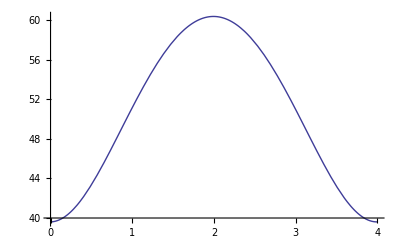

```mathematica
Plot[Abs[rr[100 I,z+I]],{z,0,4}]
```

```mathematica
N@I^(1+I)
```

1.2729×10^-17+0.20788 ⅈ

```mathematica
(-2s+1/(2s))
```

1/(2 s)-2 s

```mathematica
ar[n_,s_]:=-2n+(-2s+1/(2s))Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]
```

```mathematica
ar[10000,N@Im@ZetaZero@1]
```

4.89495×10^59+0. ⅈ

```mathematica
hsub2y[n_,s_]:=Sum[(n/j)^(1/2)(2s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]
hsub2ya[n_,s_]:=Sum[(n/j)^(1/2)(Cos[s Log[n/j]]- (1/2/s)Sin[s Log[n/j]]),{j,1,n}]
hadd2y[n_,s_]:=-2n+Sum[(n/j)^(1/2)( Cos[s Log[n/j]]+ 2 s Sin[s Log[n/j]]),{j,1,n}]
bh[n_,s_]:=-2n+Sum[(n/j)^(1/2)( Cos[s Log[n/j]]+ 2 s Sin[s Log[n/j]]),{j,1,n}]-Sum[(n/j)^(1/2)(Cos[s Log[n/j]]- (1/2/s)Sin[s Log[n/j]]),{j,1,n}]
bh2[n_,s_]:=-2n+Sum[(n/j)^(1/2)( 2 s Sin[s Log[n/j]]),{j,1,n}]-Sum[(n/j)^(1/2)(- (1/2/s)Sin[s Log[n/j]]),{j,1,n}]
bh3[n_,s_]:=-2n+(2 s+1/(2s))Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]
bhx[n_,s_]:=-2n/(2s)-s-1/(4 s)+(2 s+1/(2s))Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]
bh3a[n_,s_]:=-(4 s n)/(1+4 s^2)+Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]
bhxa[n_,s_]:=-(2 n)/(1+4 s^2)-1/2+Sum[(n/j)^(1/2)Cos[s Log[n/j]],{j,1,n}]
```

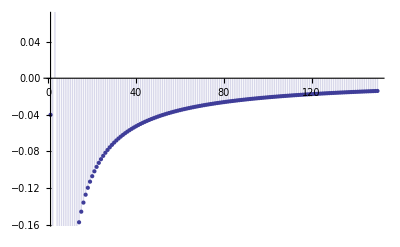

```mathematica
DiscretePlot[Re@bh3a[n,N@Im@ZetaZero@3],{n,1,150}]
```

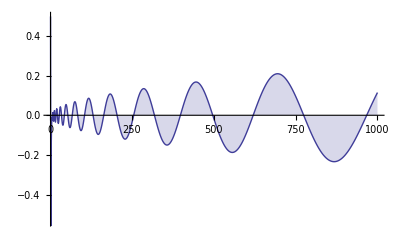

```mathematica
DiscretePlot[Re@bhxa[n,N@Im@ZetaZero@1+.01],{n,1,1000}]
```

```mathematica
1/(n^(1/2-s))
```

n^(-1/2+s)

```mathematica
FullSimplify[(s+(1/(4s)))/(2s+1/(2s))]
```

1/2

```mathematica
FullSimplify[2n/(2s)/(2s+1/(2s))]
```

(2 n)/(1+4 s^2)

```mathematica
FullSimplify[(-s-1/(4 s))/(2 s+1/(2s))]
```

-1/2

```mathematica
FullSimplify[(-2n/(2s))/(2 s+1/(2s))]
```

-(2 n)/(1+4 s^2)

```mathematica
FullSimplify[-(2 n)/(1+4 s^2)-1/2/.s->Im@ZetaZero@3]
```

-1/2-(2 n)/(1+4 Im[ZetaZero[3]]^2)

```mathematica
FullSimplify[-n/( s+1/(4s))]
```

-(4 n s)/(1+4 s^2)

```mathematica
Expand[(1/2-s I)(1/2+s I)]
```

1/4+s^2

```mathematica
gadd[n_,s_]:=-2n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
gsub[n_,s_]:=(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
gsubi[n_,s_]:=((1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))/(2 s)
gsubi2[n_,s_]:=((1/2+1/(4s))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(1/2-1/(4 s))(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))
gall[n_,s_]:=-2n+(1/2+s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(1/2-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])-((1/2+1/(4s))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(1/2-1/(4 s))(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))
gall2[n_,s_]:=-2n+(s)(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])-((1/(4s))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(-1/(4 s))(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))
gall3[n_,s_]:=-2n+s(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-s(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])-((1/(4s))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-1/(4 s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))
gall4[n_,s_]:=-2n+(s-(1/(4s)))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])+(1/(4 s)-s)(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
gall5[n_,s_]:=-2n+(s-(1/(4s)))(Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-(s-1/(4 s))(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s])
gall6[n_,s_]:=-2n+(s-1/(4 s))((Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s])-(Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2+s) Zeta[1/2+s]))
gall7[n_,s_]:=(-2n)/(s-1/(4 s))+Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s]-Sum[(n/j)^(1/2+s),{j,1,n}]+n^(1/2+s) Zeta[1/2+s]
gall8[n_,s_]:=(8 s)/(1-4 s^2)n+Sum[(n/j)^(1/2-s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s]-Sum[(n/j)^(1/2+s),{j,1,n}]+n^(1/2+s) Zeta[1/2+s]
gall9[n_,s_]:=(8 s)/(1-4 s^2)n+Sum[(n/j)^(1/2-s),{j,1,n}]-Sum[(n/j)^(1/2+s),{j,1,n}]-n^(1/2-s) Zeta[1/2-s]+n^(1/2+s) Zeta[1/2+s]
gall10[n_,s_]:=-(8 s)/(1-4 s^2)n+2Sum[(n/j)^(1/2)Sinh[s Log[n/j]],{j,1,n}]+n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s]
```

```mathematica
gall10[13000,-1.3+3I]
```

0.0000167228-0.0000384691 ⅈ

```mathematica
Expand@FullSimplify[(1/2+s)/(2 s)]
```

1/2+1/(4 s)

```mathematica
(1/2+1/(4 s))
```

1/2+1/(4 s)

```mathematica
Expand[(1/2-s)/(2 s)]
```

```mathematica
(-1/2+1/(4 s))
```

```mathematica
FullSimplify[(-2n)/(s-1/(4 s))]
```

(8 n s)/(1-4 s^2)

```mathematica
Expand[(1-2s)(1+2s)]
```

1-4 s^2

```mathematica
Sum[(n/j)^(1/2-s),{j,1,n}]-Sum[(n/j)^(1/2+s),{j,1,n}]/.n->100/.s->.2+4I
```

-10.6959-43.6213 ⅈ

```mathematica
-2Sum[(n/j)^(1/2)Sinh[s Log[n/j]],{j,1,n}]/.n->100/.s->.2+4I
```

-10.6959-43.6213 ⅈ

```mathematica
call10[n_,s_]:=-4/(1-4 s^2)n-1+2Sum[(n/j)^(1/2)Cosh[s Log[n/j]],{j,1,n}]-n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s]
```

```mathematica
call10[30000,-.75+40 I]
```

-2.77383×10^-6+7.567×10^-10 ⅈ

```mathematica
FullSimplify[-4/(1-4 s^2)n-1+2Sum[(n/j)^(1/2)Cosh[s Log[n/j]],{j,1,n}]-n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s]/.s->1/2-s]
```

-1+n/((-1+s) s)+2 ∑_(j=1)^n √(n/j) Cosh[(1/2-s) Log[n/j]]-n^(1-s) Zeta[1-s]-n^s Zeta[s]

```mathematica
FullSimplify[-(8 s)/(1-4 s^2)n+2Sum[(n/j)^(1/2)Sinh[s Log[n/j]],{j,1,n}]+n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s]/.s->1/2-s]
```

(n-2 n s)/((-1+s) s)+2 ∑_(j=1)^n √(n/j) Sinh[(1/2-s) Log[n/j]]-n^(1-s) Zeta[1-s]+n^s Zeta[s]

```mathematica
-4/(1-4 s^2)n-1+2Sum[(n/j)^(1/2)Cosh[s Log[n/j]],{j,1,n}]-n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s]/.s->s I
```

-1-(4 n)/(1+4 s^2)+2 ∑_(j=1)^n √(n/j) Cos[s Log[n/j]]-n^(1/2-ⅈ s) Zeta[1/2-ⅈ s]-n^(1/2+ⅈ s) Zeta[1/2+ⅈ s]

```mathematica
Expand[(-(8 s)/(1-4 s^2)n+2Sum[(n/j)^(1/2)Sinh[s Log[n/j]],{j,1,n}]+n^(1/2-s) Zeta[1/2-s]-n^(1/2+s) Zeta[1/2+s])I^3]/.s->s I
```

-(8 n s)/(1+4 s^2)-2 ⅈ ∑_(j=1)^n ⅈ √(n/j) Sin[s Log[n/j]]-ⅈ n^(1/2-ⅈ s) Zeta[1/2-ⅈ s]+ⅈ n^(1/2+ⅈ s) Zeta[1/2+ⅈ s]

```mathematica
ComplexExpand[Re[n^(1+A+f I)/(1+A+f I)]]/.Arg[n]->0
```

((n^2)^((1+A)/2) Cos[1/2 f Log[n^2]])/((1+A)^2+f^2)+(A (n^2)^((1+A)/2) Cos[1/2 f Log[n^2]])/((1+A)^2+f^2)+(f (n^2)^((1+A)/2) Sin[1/2 f Log[n^2]])/((1+A)^2+f^2)

```mathematica
-2/(1+4(N@Im@ZetaZero@1)^2)
```

-0.00249949

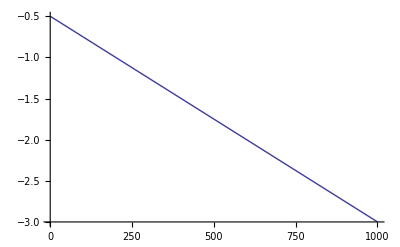

```mathematica
Plot[-2/(1+4(N@Im@ZetaZero@1)^2)n-1/2,{n,1,1000}]
```

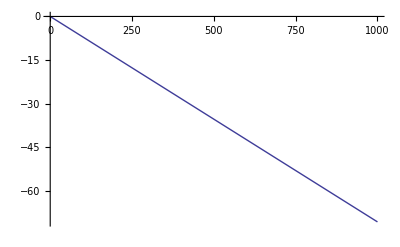

```mathematica
Plot[-(4 N@Im@ZetaZero@1)/(1+4(N@Im@ZetaZero@1)^2)n,{n,1,1000}]
```

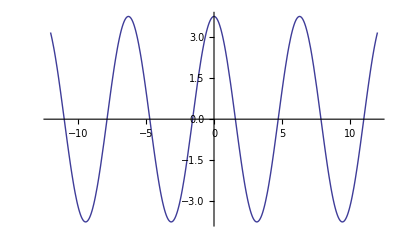

```mathematica
Plot[Re[Cos[s+2I]],{s,-12,12}]
```

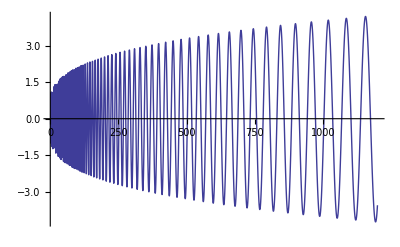

```mathematica
Plot[Re[Sin[Log[s] (100+.3I)]],{s,1,1200}]
```

```mathematica
Sin[3.+2I]
```

0.530921-3.59056 ⅈ

```mathematica
Sin[3.+2I+2Pi]
```

0.530921-3.59056 ⅈ

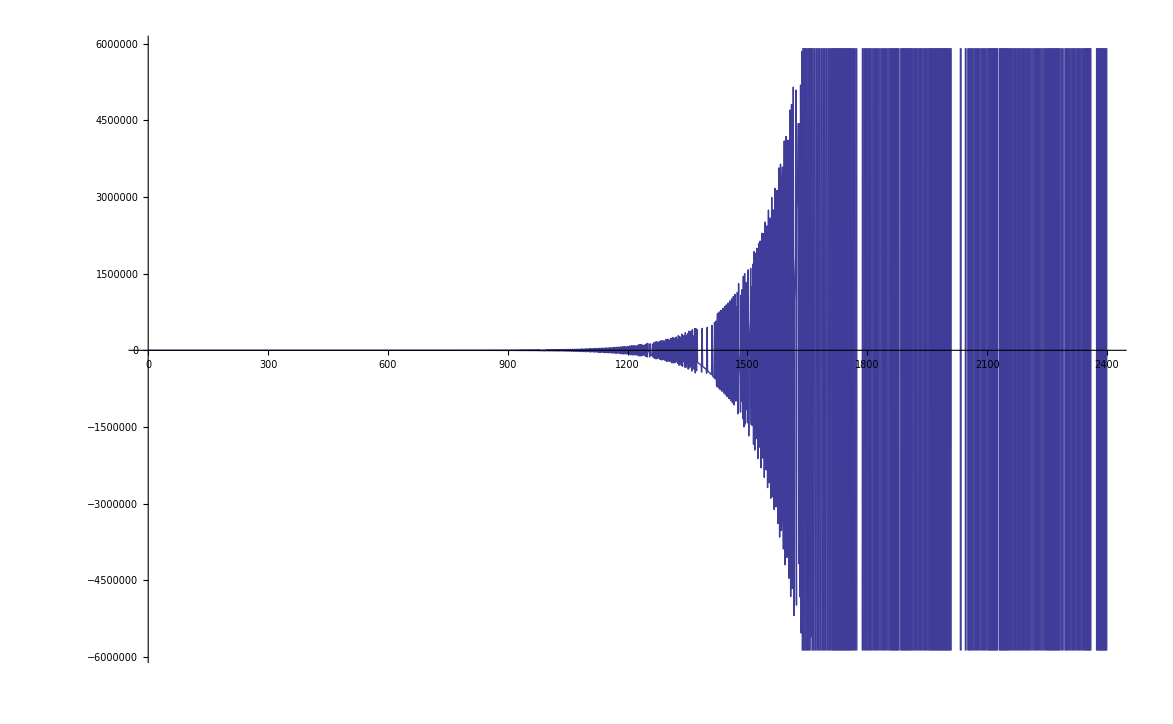

```mathematica
Plot[Im[Cos[(10-.01I)s]],{s,0,2400}]
```

```mathematica
bebo[n_,s_]:={-4s/(1+4s^2)n,Table[(n/j)^(1/2)Sin[s Log[n/j]],{j,n-40,n}]//TableForm}
```

```mathematica
N@bebo[10^3,Im@ZetaZero@1+.001I]
```

{-70.6593+0.00498649 ⅈ,0.556768+0.0000349184 ⅈ
0.543837+0.0000343322 ⅈ
0.530815+0.0000337231 ⅈ
0.517706+0.0000330919 ⅈ
0.504512+0.0000324391 ⅈ
0.491238+0.0000317653 ⅈ
0.477885+0.0000310712 ⅈ
0.464458+0.0000303574 ⅈ
0.450959+0.0000296246 ⅈ
0.437392+0.0000288734 ⅈ
0.42376+0.0000281044 ⅈ
0.410065+0.0000273183 ⅈ
0.396312+0.0000265158 ⅈ
0.382504+0.0000256975 ⅈ
0.368643+0.000024864 ⅈ
0.354733+0.000024016 ⅈ
0.340777+0.0000231542 ⅈ
0.326778+0.0000222791 ⅈ
0.312739+0.0000213915 ⅈ
0.298664+0.0000204921 ⅈ
0.284554+0.0000195814 ⅈ
0.270415+0.0000186601 ⅈ
0.256248+0.0000177289 ⅈ
0.242057+0.0000167884 ⅈ
0.227845+0.0000158392 ⅈ
0.213614+0.0000148821 ⅈ
0.199368+0.0000139177 ⅈ
0.185111+0.0000129465 ⅈ
0.170844+0.0000119693 ⅈ
0.156571+0.0000109866 ⅈ
0.142295+9.99922×10^-6 ⅈ
0.128018+9.00765×10^-6 ⅈ
0.113745+8.01258×10^-6 ⅈ
0.0994767+7.01461×10^-6 ⅈ
0.0852173+6.01438×10^-6 ⅈ
0.0709693+5.01251×10^-6 ⅈ
0.0567356+4.00962×10^-6 ⅈ
0.042519+3.00631×10^-6 ⅈ
0.0283223+2.00321×10^-6 ⅈ
0.0141484+1.0009×10^-6 ⅈ
0.+0. ⅈ}

```mathematica
peo[n_,z_]:=Sum[(n/j)^(1/2) Cosh[z Log[n/j]-ArcCoth[2z]],{j,1,n}]
```

```mathematica
peo[100000,-.5+N@ZetaZero@1+.2I]
```

$Aborted

```mathematica
bbo[n_,s_]:=-4s/(1+4s^2)n+Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]
bba[n_,s_]:=Abs[-4s/(1+4s^2)n]-Abs[Sum[(n/j)^(1/2)Sin[s Log[n/j]],{j,1,n}]]
```

```mathematica
bbo[10000,N@Im@ZetaZero@1]
```

-0.000117789

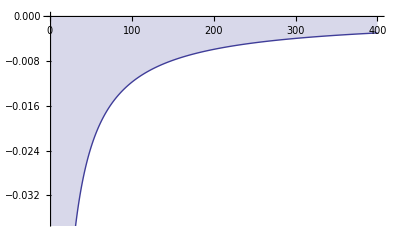

```mathematica
DiscretePlot[Re@bbo[n,N@Im@ZetaZero@1],{n,1,400}]
```

```mathematica
-Integrate[Sin[z Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[(4 z)/(1+4 z^2),-1/2<Im[z]<1/2]

```mathematica
Limit[1/n Sum[(n/j)^(1/2) Sin[z Log[n/j]],{j,1,n}],n->Infinity]
```

Limit[(∑_(j=1)^n √(n/j) Sin[z Log[n/j]])/n,n→∞]

```mathematica
-Integrate[Cos[z Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-2/(1+4 z^2),z∈Reals]

```mathematica
-Integrate[Tan[z Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(-4 ⅈ z+PolyGamma[0,1/2-ⅈ/(8 z)]-PolyGamma[0,-ⅈ/(8 z)])/(2 z),Im[z]<0]

```mathematica
-n^(1/2)-n^(-1/2)/.n->10.3
```

-3.52095

```mathematica
-E^(1/2 Log[n])-E^(-1/2 Log[n])/.n->10.3
```

-3.52095

```mathematica
-2Cosh[(1/2)Log[n]]/.n->10.3
```

-3.52095

```mathematica
feh[n_,s_]:=-2 Cosh[1/2Log[n]]+Sum[j^(-1/2)(1/2 Cos[s Log[n/j]]+s Sin[s Log[n/j]]),{j,1,n}]
feha[n_,s_]:=-2 Cosh[1/2Log[n]]
```

```mathematica
feh[100000,N@Im@ZetaZero@1]
```

-0.00237224

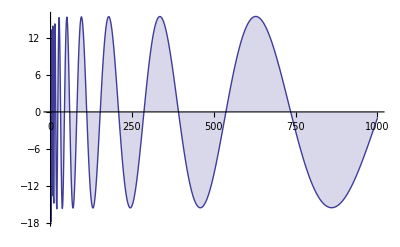

```mathematica
DiscretePlot[Re@feh[n,10],{n,1,1000}]
```

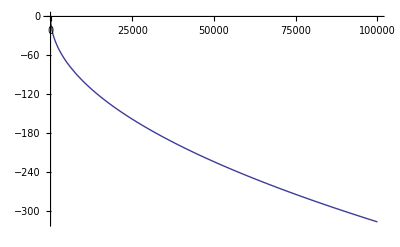

```mathematica
Plot[feha[n,1],{n,1,100000}]
```

```mathematica
pla[n_,s_]:=Sum[(n j)^(-1/2) Sin[s Log[n/j]],{j,1,n}]
```

```mathematica
po[n_]:=1/n Sum[Sin[j/n],{j,1,n}]
```

```mathematica
N@Integrate[Sin[x],{x,0,1}]
```

0.459698

```mathematica
po[1000000.]
```

0.459698

```mathematica
pla[n_,s_]:=(1/n)Sum[(j/n)^s,{j,1,n}]
```

```mathematica
n Integrate[x^s,{x,0,1}]
```

ConditionalExpression[n/(1+s),Re[s]>-1]

```mathematica
pla[1000,.5]
```

0.66716

```mathematica
Integrate[ (2 s Cos[s Log[x]]-Sin[ s Log[x]])/(x^(1/2)),{x,0,1}]
```

ConditionalExpression[(8 s)/(1+4 s^2),s∈Reals]

```mathematica
pn[n_,s_]:=n (1/n)Sum[(j/n)^(-1/2)(2  s Cos[s Log[j/n]]+Sin[s Log[j/n]]),{j,1,n}]
```

```mathematica
pn[100,N@Im@ZetaZero@1 ]
```

14.1347

```mathematica
Integrate[x^(-1/2)(2  s Cos[s Log[x]]+Sin[s Log[x]]),{x,0,1}]
```

ConditionalExpression[0,s∈Reals]

```mathematica
Integrate[x^(-1/2)(2  s Cos[s Log[x]]),{x,0,1}]
```

ConditionalExpression[(4 s)/(1+4 s^2),s∈Reals]

```mathematica
Integrate[x^(-1/2)(Sin[s Log[x]]),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
pr[n_,s_]:=n (1/n Sum[(j/n)^(-1/2+s),{j,1,n}])
```

```mathematica
pr[100,.5+I]
```

50.0839-50.0406 ⅈ

```mathematica
Integrate[x^(-1/2+s),{x,0,1}]
```

ConditionalExpression[2/(1+2 s),Re[s]>-1/2]

```mathematica
FullSimplify[(1/2+s)(2/(1+2s))]
```

1

```mathematica
pb[n_,s_]:=Sum[j^-s,{j,1,n}]-Integrate[j^-s,{j,0,n}]
pbc[n_,s_]:=Sum[E^-(s Log[j]),{j,1,n}]-Integrate[E^-(s Log[j]),{j,0,n}]
pbd[n_,s_]:=Sum[E^-(s Log[j]),{j,1,n}]-Integrate[E^-(s Log[j]),{j,0,n}]
pbe[n_,A_, f_]:=Sum[j^-A (Cos[f Log[j]]),{j,1,n}]-Integrate[j^-A (Cos[f Log[j]]),{j,0,n}]+I (Sum[j^-A ( Sin[f Log[j]]),{j,1,n}]-Integrate[j^-A (Sin[f Log[j]]),{j,0,n}])
pbf[n_,A_, f_]:=Sum[j^-A (Cos[f Log[j]]),{j,1,n}]-Integrate[j^-A (Cos[f Log[j]]),{j,0,n}]+I (Sum[j^-A ( Sin[f Log[j]]),{j,1,n}]-Integrate[j^-A (Sin[f Log[j]]),{j,0,n}])
```

```mathematica
pbe[10000,.5,10]
```

1.54189+0.111262 ⅈ

```mathematica
pb[10000,.5+10I]
```

1.54189-0.111262 ⅈ

```mathematica
Zeta[.5+10I]
```

1.5449-0.115336 ⅈ

```mathematica
Integrate[j^-A (Cos[f Log[j]]),{j,0,n}]
```

ConditionalExpression[(n^-A (-(-1+A) n Cos[f Log[n]]+0 Sin[f (-∞)]+f n Sin[f Log[n]]))/((-1+A)^2+f^2),Re[A]<1]

```mathematica
Integrate[j^-A (Sin[f Log[j]]),{j,0,n}]
```

ConditionalExpression[(n^-A (-f n Cos[f Log[n]]+0 Sin[f (-∞)]-(-1+A) n Sin[f Log[n]]))/((-1+A)^2+f^2),Re[A]<1]

```mathematica
Integrate[j^(-A-f I),{j,0,n}]
```

ConditionalExpression[-n^(1-A-ⅈ f)/(-1+A+ⅈ f),Re[A]<1+Im[f]]

```mathematica
ab[n_,s_]:=(1/n)Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]
abb[s_]:=4s/(1+4s^2)
```

```mathematica
ab[100000,20.+.1I]
```

0.0511243-0.0050391 ⅈ

```mathematica
abb[20.+.1I]
```

0.0499675-0.000249526 ⅈ

```mathematica
s1[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I) Zeta[1/2+s I]- n^(1/2-s I) Zeta[1/2-s I])
xi[s_]:=1/2 π^(-s/2) (-1+s) s Gamma[s/2] Zeta[s]
zet[s_]:=xsi[s]/(1/2 π^(-s/2) (-1+s) s Gamma[s/2])
s2[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2+s I)((2 π^(1/2 (1/2+ⅈ s)) xi[1/2+ⅈ s])/((-1/2+ⅈ s) (1/2+ⅈ s) Gamma[1/2 (1/2+ⅈ s)]))- n^(1/2-s I)((2 π^(1/2 (1/2-ⅈ s)) xi[1/2-ⅈ s])/((-1/2-ⅈ s) (1/2-ⅈ s) Gamma[1/2 (1/2-ⅈ s)])))

s3[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I( ((n^(1/2+s I)2 π^(1/2 (1/2+ⅈ s)) xi[1/2+ⅈ s])/((-1/2+ⅈ s) (1/2+ⅈ s) Gamma[1/2 (1/2+ⅈ s)]))- ((n^(1/2-s I)2 π^(1/2 (1/2-ⅈ s)) xi[1/2-ⅈ s])/((-1/2-ⅈ s) (1/2-ⅈ s) Gamma[1/2 (1/2-ⅈ s)])))
s4[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I( n^(1/2)xi[1/2+ⅈ s](((n^(s I)2 π^(1/2 (1/2+ⅈ s)))/((-1/4-s^2) Gamma[1/2 (1/2+ⅈ s)]))- ((n^(-s I)2 π^(1/2 (1/2-ⅈ s)))/((-1/4-s^2) Gamma[1/2 (1/2-ⅈ s)]))))
s5[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I(2 n^(1/2)xi[1/2+ⅈ s]/(-1/4-s^2) (((n^(s I)π^(1/4+ⅈ s/2))/Gamma[1/2 (1/2+ⅈ s)])- ((n^(-s I)π^(1/4-ⅈ s/2))/Gamma[1/2 (1/2-ⅈ s)])))
s6[n_,s_]:=-8s/(1+4s^2)n+2 Sum[(n/j)^(1/2) Sin[s Log[n/j]],{j,1,n}]+I(2 n^(1/2)π^(1/4)xi[1/2+ⅈ s]/(-1/4-s^2) (((n^(s I)π^(ⅈ s/2))/Gamma[1/2 (1/2+ⅈ s)])- ((n^(-s I)π^(-ⅈ s/2))/Gamma[1/2 (1/2-ⅈ s)])))
```

```mathematica
s6[10000,-.5+.1I]
```

8.33329×10^-6-1.66666×10^-6 ⅈ

```mathematica
1/2 s(s-1)Pi^(-s/2)Gamma[s/2]Zeta[s]
```

1/2 π^(-s/2) (-1+s) s Gamma[s/2] Zeta[s]

```mathematica
zet[1/2-s I]
```

```mathematica
(2 π^(1/2 (1/2-ⅈ s)) xi[1/2-ⅈ s])/((-1/2-ⅈ s) (1/2-ⅈ s) Gamma[1/2 (1/2-ⅈ s)])
```

```mathematica
xi[(2+.3I)]
```

0.52241+0.0108274 ⅈ

```mathematica
zet[1/2+s I]
```

```mathematica
(2 π^(1/2 (1/2+ⅈ s)) xi[1/2+ⅈ s])/((-1/2+ⅈ s) (1/2+ⅈ s) Gamma[1/2 (1/2+ⅈ s)])
```

```mathematica
Gamma[1/2 (1/2+ⅈ s)]/.s->(-.5+.1I)
```

1.57144+2.26644 ⅈ

```mathematica
Expand[(-1/2+I s)(1/2+I s)]
```

-1/4-s^2

```mathematica
Expand[(-1/2-I s)(1/2-I s)]
```

-1/4-s^2